# Computational X-Plorations

https://datarepository.wolframcloud.com/

## COVID-19

Wolfram's X-Ploration

### How to...

```mathematica
ResourceObject["Epidemic Data for Novel Coronavirus COVID-19"]
```

ResourceObject[…]

```mathematica
df = ResourceData["Epidemic Data for Novel Coronavirus COVID-19"];
```

## Crucial Topics

Variable

List

Functions

Dataset

Control Flow

Objects

Graphics

### Dataset

```mathematica
df[1;;5,All]
```

Dataset[<>]

### Timeseries

```mathematica
df[1,"Deaths"]
```

TimeSeries[…]

#### Let's learn about properties.

```mathematica
Manipulate[df[1,"Deaths"][n],{n,df[1,"Deaths"]["Properties"]}]
```

## Introduction

#### A variable

```mathematica
myVariable = df[1,"Country"]
```

United States

```mathematica
timeFrame = df[1,"Deaths"]["DatePath"];
```

```mathematica
short = timeFrame[[1;;3]]
```

{{Wed 22 Jan 2020 00:00:00GMT-6.,0},{Thu 23 Jan 2020 00:00:00GMT-6.,0},{Fri 24 Jan 2020 00:00:00GMT-6.,0}}

```mathematica
short[[1]]
```

```mathematica
short[[1,1]]
```

```mathematica
short //Dimensions
```

```mathematica
short//MatrixForm
```

### Lists: everything in Mathematica is a list

```mathematica
timeFrame[[1;;3]]
```

{{Wed 22 Jan 2020 00:00:00GMT-6.,0},{Thu 23 Jan 2020 00:00:00GMT-6.,0},{Fri 24 Jan 2020 00:00:00GMT-6.,0}}

```mathematica
numbers = timeFrame[[All,2]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,10,13,16,34,42,60,117,158,210,285,385,527,728,965,1218,1550,1941,2373,2935,3565,4159,4698,5489,6268,7067,7867,8627,9385,10058,10842,11617,14832,17131,17671,18298,18611,19104,19413,20973,21411,22009,22269}

#### Anonymous & Pure Functions

```mathematica
Total[numbers]
```

314936

```mathematica
Mean[numbers]
```

292667/95

```mathematica
Quartiles[numbers]
```

{0,0,2654}

```mathematica
Max[numbers]
```

22269

```mathematica
Min[numbers]
```

0

```mathematica
#⟦1⟧&/@short
```

{Wed 22 Jan 2020 00:00:00GMT-6.,Thu 23 Jan 2020 00:00:00GMT-6.,Fri 24 Jan 2020 00:00:00GMT-6.}

```mathematica
#⟦2⟧&/@short
```

{0,0,0}

```mathematica
#2&@@@timeFrame
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,10,13,16,34,42,60,117,158,210,285,385,527,728,965,1218,1550,1941,2373,2935,3565,4159,4698,5489,6268,7067,7867,8627,9385,10058,10842,11617,14832,17131,17671,18298,18611,19104,19413,20973,21411,22009,22269}

### Control Flow

```mathematica
If[
MissingQ[df[2,"AdministrativeDivision"]],
df[2,"Country"],
df[2,"AdministrativeDivision"]
]
```

Spain

#### Creating a predicate

```mathematica
if[n_Integer]:=If[
MissingQ[df[n,"AdministrativeDivision"]],
df[n,"Country"],
df[n,"AdministrativeDivision"]
];
```

## How to create apps

### Time Series

```mathematica
t1 =
```

TimeSeries[…]

```mathematica
t2 =
```

TimeSeries[…]

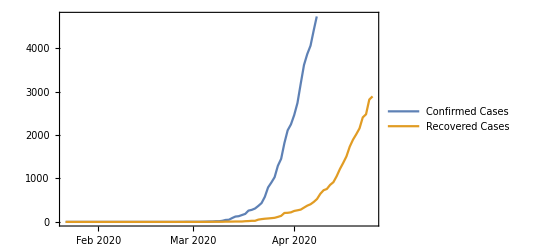

```mathematica
DateListPlot[{},PlotLegends->{"Confirmed Cases","Recovered Cases"}]
```

#### Creating an applet

```mathematica
Manipulate[
GraphicsRow[{
DateListPlot[{df[n,"ConfirmedCases"],df[n,"RecoveredCases"]},
PlotLabel->if[n],
PlotLegends->{"Confirmed Cases","Recovered Cases"}],
GeoGraphics[GeoMarker[df[n,"GeoPosition"]]]
},ImageSize->Large],
{n,1,Length[df],1}
]
```

### Different Plots

#### Create a geographical plot

```mathematica
countryMap[n_Integer] := GeoGraphics[{GeoMarker[df[n,"GeoPosition"]],Polygon[df[n,"Country"]]}];
```

#### Refactor all dates

```mathematica
allDates[n_Integer] := DateString[#,{"Month","/","YearShort"}]&/@df[n,"Deaths"]["Dates"];
```

#### Create a bar chart

```mathematica
bars[n_Integer] := BarChart[{#2,#1}&@@@df[n,"Deaths"]["DatePath"] ,
PlotLabel-> if[n],
ChartLabels -> Placed[allDates[n], Below, Rotate[#, Pi/2.4] &]];
```

#### Create an applet

```mathematica
Manipulate[
GraphicsRow[{
bars[n],
 countryMap[n]
 },ImageSize->Full], {n,1,Length[df],1} 
]
```

### Further explorations....

```mathematica
df[1,"Country"]->Total[df[1,"ConfirmedCases"]["DatePath"]⟦All,2⟧]
```

United States→5256165

```mathematica
map = df[#,"Country"]->Total[df[#,"ConfirmedCases"]["DatePath"]⟦All,2⟧]&/@Range[Length[df]];
```

```mathematica
map[[1;;3]]
```

{United States→5256165,Spain→4959878,Italy→5131965}

```mathematica
Manipulate[
geo[map⟦1;;n⟧,ImageSize->Full],
{n,5,Length[map],1},
{geo,{GeoRegionValuePlot,GeoBubbleChart,GeoSmoothHistogram}}
]
```

## Machine Learning

```mathematica
RandomSample[ResourceData["FER-2013"],10]
```

```mathematica
allData = RandomSample[ResourceData["FER-2013"],100];
```

```mathematica
trainingData = Take[allData,80];
```

```mathematica
testData = Drop[allData,80];
```